Auxiliary notebook to get the coordinates of the patchy particles.
Also analyse the potentials and energy wells.

#### Coordinates of the Patchy particles

a is the length of the tetrahedron.

```mathematica
Vertex = Function[a,a {{0,0,√(2/3)-1/(2 √6)},{-1/(2 √3),-1/2,-1/(2 √6)},{-1/(2 √3),1/2,-1/(2 √6)},{1/(√3),0,-1/(2 √6)}}]
```

Function[a,a {{0,0,√(2/3)-1/(2 √6)},{-1/(2 √3),-1/2,-1/(2 √6)},{-1/(2 √3),1/2,-1/(2 √6)},{1/(√3),0,-1/(2 √6)}}]

```mathematica
centers = Vertex[3/4]
N[centers,2]
Graphics3D[
	Append[
		Table[Sphere[centers[[i]],0.25],{i,Length[centers]}],
		{Opacity[0.5],Sphere[{0,0,0},0.5]}
		]
	]
```

{{0,0,3/4 (√(2/3)-1/(2 √6))},{-(√3)/8,-3/8,-(√(3/2))/8},{-(√3)/8,3/8,-(√(3/2))/8},{(√3)/4,0,-(√(3/2))/8}}

{{0,0,0.46},{-0.22,-0.38,-0.15},{-0.22,0.38,-0.15},{0.43,0,-0.15}}

-Graphics3D-

#### Stuff of the potentials

σ is the radius of the particle :)

```mathematica
σCL = 0.5;
σMO = 0.5;
σPA = 0.25;
σPB = 0.25;
rcCL = 2^(1/6)σCL;
rcMO = 2^(1/6)σMO;
rcPA = 2^(1/6)σPA;
rcPB = 2^(1/6)σPB;
```

0.561231

```mathematica
LJP[ϵ_,σ_,r_]:= 4 ϵ((σ/r)^12 - (σ/r)^6)
```

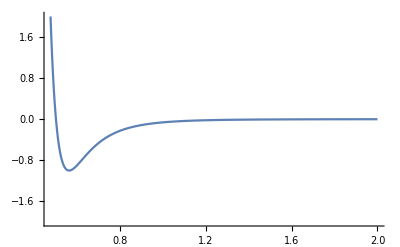

```mathematica
Module[{ep=1,sig=0.5,rm=2},
	Plot[LJP[ep,sig,s],{s,0,rm},
	PlotRange->{All,{-2 ep, 2 ep}}
	]
]
```